```mathematica
(* This is necessary for removing previously defined variables *)
ClearAll["Global`*"]
```

## Misc Modules

```mathematica
stripList[lst_]:=Module[{lst2},
lst2 = List[];
Do[AppendTo[lst2,Last[lst[[ii]]]],{ii,Length[lst]}];
Return[lst2]]
```

```mathematica
a=List[{1},{2},{3}]
stripList[a]
```

{{1},{2},{3}}

{1,2,3}

```mathematica
(* Write Module to Count number of roots in a function *)
(* From https://www.physicsforums.com/threads/find-all-roots-of-an-interpolating-function-in-mathematica.612362/ *)
countZeros[ifun_,xmin_,xmax_,dx_] := Module[{zeros,numZeros},
zeros = Union[Table[x/.FindRoot[ifun[x]==0.,{x,xInit,xmin,xmax}],{xInit,xmin+dx,xmax-dx,dx}],SameTest->(Abs[#1-#2]<10^-4&)];
numZeros = Length[zeros];
Print[zeros];
If[Last[zeros]==xmax,If[ifun[xmax]≠0,numZeros=numZeros-1]];
If[First[zeros]==xmin,If[ifun[xmin]≠0,numZeros=numZeros-1]];
Return[numZeros]]
```

```mathematica
f[x_]:=x^4-x^2
countZeros[f,-2,2,0.1]
```

{-1.,-1.01172×10^-8,1.}

3

```mathematica
countAllZeros[ifun_,xmin_,xmax_,dx_,hardLim_]:=Module[{z,ztot,num,ii},
z=countZeros[ifun,xmin,xmax,dx];
Print["number of zeros for the function is ",z];
ztot=z;
If[z==0,num=0,num=1];
ii=1;
While[True,
f[x_]=D[ifun[x],{x,ii}];
If[f[x_]==0,Break[]];
z=countZeros[f,xmin,xmax,dx];
Print["number of zeros for ",ii,"th derivative is ",z];
ztot=ztot+z;
If[z==0,num++];
If[num≥2,Break[]];
If[ii≥hardLim,Break[]];
ii++];
Return[ztot]]
```

```mathematica
f[x_]:=x^4-x^2
countAllZeros[f,-10,10,0.1,1]
```

{-1.,-1.01172×10^-8,1.}

number of zeros for the function is 3

{-0.707107,-1.17155×10^-19,0.707107}

number of zeros for 1th derivative is 3

6

## Cosmology Calculation Modules

```mathematica
findZϵsr[v_,vp_,ϕsol_,nmin_,nmax_,dn_,hardLim_]:=Module[{ϵsr,f,z,num,ii,ztot},
ϵsr[x_]:=1/2*(vp[x]/v[x])^2;
f[n_]:=ϵsr[ϕ[n]]/.ϕsol;
Print[Plot[Evaluate[f[n]],{n,nmin,nmax},AxesLabel->{N,"ϵsr"},PlotRange->{-1,1}]];
z=countZeros[f,nmin,nmax,dn];
Print["number of zeros for ϵsr is ",z];
ztot=z;
If[z==0,num=0,num=1];
ii=1;
While[True,
f[n_]=D[ϵsr[ϕ[n]]/.ϕsol,{n,ii}];
Print[Plot[Evaluate[f[n]],{n,nmin,nmax},AxesLabel->{N,ii},PlotRange->{-1,1}]];
If[f[n_]==0,Break[]];
z=countZeros[f,nmin,nmax,dn];
Print["number of zeros for ",ii,"th derivative of ϵ is ",z];
ztot=ztot+z;
If[z==0,num++];
If[num≥2,Break[]];
If[ii≥hardLim,Break[]];
ii++];
Return[ztot]]
```

```mathematica
findZϵ[v_,ϕsol_,nmin_,nmax_,dn_,hardLim_]:=Module[{hsq,ϵ,f,z,num,ii,ztot},
hsq[n_]:=v[ϕ[n]]/(3-1/2*ϕ'[n]^2);
ϵ[n_] = Evaluate[3*ϕ'[n]^2/(ϕ'[n]^2+2*v[ϕ[n]]/hsq[n])];
f[n_] = ϵ[n]/.ϕsol;
Print[Plot[Evaluate[f[n]],{n,nmin,nmax},AxesLabel->{N,"ϵ"},PlotRange->{-1,1}]];
z=countZeros[f,nmin,nmax,dn];
Print["number of zeros for ϵ is ",z];
ztot=z;
If[z==0,num=0,num=1];
ii=1;
While[True,
f[n_]=D[ϵ[ϕ[n]],{n,ii}]/.ϕsol;
Print[Plot[Evaluate[f[n]],{n,nmin,nmax},AxesLabel->{N,ii},PlotRange->{-1,1}]];
If[f[n_]==0,Break[]];
z=countZeros[f,nmin,nmax,dn];
Print["number of zeros for ",ii,"th derivative of ϵ is ",z];
ztot=ztot+z;
If[z==0,num++];
If[num≥2,Break[]];
If[ii≥hardLim,Break[]];
ii++];
Return[ztot]]
```

```mathematica
findZη[v_,vpp_,ϕsol_,nmin_,nmax_,dn_,hardLim_]:=Module[{ηsr,f,z,num,ii,ztot},
ηsr[n_]:=vpp[ϕ[n]]/v[ϕ[n]];
f[n_]:=ηsr[ϕ[n]]/.ϕsol;
Print[Plot[Evaluate[f[n]],{n,nmin,nmax},AxesLabel->{N,"ηsr"},PlotRange->{-1,1}]];
z=countZeros[f,nmin,nmax,dn];
Print["number of zeros for ηsr is ",z];
ztot=z;
If[z==0,num=0,num=1];
ii=1;
While[True,
f[n_]=D[ηsr[ϕ[n]]/.ϕsol,{n,ii}];
Print[Plot[Evaluate[f[n]],{n,nmin,nmax},AxesLabel->{N,ii},PlotRange->{-1,1}]];
If[f[n_]==0,Break[]];
z=countZeros[f,nmin,nmax,dn];
Print["number of zeros for ",ii,"th derivative of η is ",z];
ztot=ztot+z;
If[z==0,num++];
If[num≥2,Break[]];
If[ii≥hardLim,Break[]];
ii++];
Return[ztot]]
```

```mathematica
findH[v_]:=Module[{h,hsq},
h[n_]:= Simplify[√(v[ϕ[n]]/(3-1/2*ϕ'[n]^2))];
hsq[n_]:=v[ϕ[n]]/(3-1/2*ϕ'[n]^2);
Return[{h,hsq}]]
```

### Find Initial Conditions for 1st Integration

```mathematica
chooseϕ0Manual[ϕ0list_]:=Module[{ϕ0index,ϕ0},
ϕ0index = Input["Enter the index for the ϕ0 you want to use: \n(Counting starts at 1)"];
ϕ0 = ϕ0list[[ϕ0index]]; 
Return[ϕ0]]
```

```mathematica
chooseϕ0Left[ϕ0list_,v_]:=Module[{ϕ0listpos,ϕ0,vacuum},
ϕ0listpos=Select[ϕ0list,#>0&];
vacuum = First[Select[ϕ0listpos,v[#]<10^-6&]];
ϕ0 = Max[Select[ϕ0listpos,#<vacuum&]];
Return[ϕ0]]
```

```mathematica
findICsr[v_,vp_,ni_,prints_]:=Module[{ϕ0list,ϕ0index,ϕ0,f,ϕiguess,ϕi1,ϕpi1,vplt,ϕ0plt,ϕiplt},
vplt = Plot[v[x],{x,-10,10},AxesLabel->{"ϕ","V"}];
(* Solve for where ϵ=1 and hence N=0 *)
ϕ0list = NSolve[vp[x]==√2*v[x],x];
ϕ0list = Values[stripList[Union[ϕ0list,NSolve[vp[x]==-√2*v[x],x]]]];
Print["ϕ0list = ",ϕ0list];
ϕ0plt = ListPlot[Transpose[{ϕ0list,v[ϕ0list]}]]; (* Transpose is Zip!! *)
Print[Show[vplt,ϕ0plt]];
ϕ0 = chooseϕ0Left[ϕ0list,v];
If[prints,Print["ϕ0 = ",ϕ0]];
(* Integrate up the hill to find the value of ϕ at ni *)
f[t_] = Integrate[v[x]/vp[x],{x,ϕ0,t}];
Print[LogLogPlot[f[t],{t,10^-5,10},AxesLabel->{"ϕ","N"}]];
(* If[prints,Print["f[t] = ",f[t]]]; *)
(*ϕi1= t/.Last[NSolve[ni==f[t],t]];*)
ϕiguess = Input["Enter a guess for ϕi1"]; 
ϕi1= t/.Last[FindRoot[ni-f[t],{t,ϕiguess}]];
Print["ϕi1 = ",ϕi1];
ϕpi1 = vp[ϕi1]/v[ϕi1] ;
ϕiplt = ListPlot[{{ϕi1,v[ϕi1]},{ϕ0,v[ϕ0]}}];
Print[Show[vplt,ϕiplt]];
Return[{ϕi1,ϕpi1}]]
```

### Find Initial Conditions for 2nd Integration

```mathematica
findICshifted[v_,ϕsol1_,prints_,plots_]:=Module[{ϵ1,n1,ϕi2,ϕpi2},
(* Find ϵ1 *)
ϵ1=findϵ[v,ϕsol1];
If[prints,Print["At n = 0",", ϵ1 = ",Evaluate[ϵ1[n]/.n->0]]];
If[plots,Print[Plot[Evaluate[ϵ1[n]],{n,nf,ni},AxesLabel->{N,"ϵ1"},PlotRange->{{nf,-nf},{0,2}},GridLines->{{-1,-1.2},{1}}]]];
(* Solve for where ϵ1[n]==1 *)
n1 = Evaluate[n/.First[FindRoot[ϵ1[n]-1,{n,n1guess}]]];
If[prints,Print["At n1 = ",n1,", ϵ1 = ",Evaluate[ϵ1[n]/.n->n1]]];
(* Find the new initial conditions *)
ϕi2 = Re[ϕ[ni2+n1]/.ϕsol1];
If[prints,Print["ϕi2 = ",ϕi2]];
ϕpi2 = Re[D[ϕ[n],n]/.ϕsol1/.n->(ni2+n1)];
If[prints,Print["ϕpi2 = ",ϕpi2]];
Return[{ϕi2,ϕpi2}]]
```

```mathematica
solveKG[hsq_,vp_,ni_,nf_,ϕi1_,ϕpi1_,plots_]:=Module[{ϕsol1},
ϕsol1 = Last@Last@NDSolve[{2*hsq[n]*ϕ''[n]+hsq[n]*(ϕ'[n])^3-6*hsq[n]*ϕ'[n]+2*vp[ϕ[n]]==0,ϕ[ni]==ϕi1,ϕ'[ni]==ϕpi1},ϕ,{n,ni,nf},InterpolationOrder->All];
If[plots,Print[Plot[Evaluate[ϕ[n]/.ϕsol1],{n,nf,ni},AxesLabel->{N,"ϕsol"},GridLines->{{-1,-1.2},{1}}]]];
Return[ϕsol1]]
```

### Find Epsilon

```mathematica
findϵ[v_,ϕsol_]:=Module[{ϕp,hsq,ϵ,η},
ϕp[n_] = D[ϕ[n],n]/.ϕsol;
hsq[n_]:=v[ϕ[n]]/(3-1/2*ϕp[n]^2)/.ϕsol;
ϵ[n_] = Evaluate[3*ϕp[n]^2/(ϕp[n]^2+2*v[ϕ[n]]/hsq[n])/.ϕsol];
(* above took out a Re[] just inside the Evaluate[] *)
(* η[n_] = D[ϵ[n],n]; *)
Return[ϵ]]
```

```mathematica
findϕsol[v_,vp_,ni_,nf_,ni2_,nf2_,n1guess_,plots_,prints_]:=Module[{h,hsq,ϕi1,ϕpi1,ϕsol1,ϕi2,ϕpi2,ϕsol2},
(* Define the hubble parameter *)
{h,hsq}=findH[v];
(* Find the slow roll initial conditions *)
{ϕi1,ϕpi1}=findICsr[v,vp,ni,prints];
(* Solve the Klein-Gordon equation for ϕ1[n] *)
ϕsol1 = solveKG[hsq,vp,ni,nf,ϕi1,ϕpi1,plots];
(* Find the new initial conditions and re-solve the KG equation *)
{ϕi2,ϕpi2}=findICshifted[v,ϕsol1,prints,plots];
ϕsol2 = solveKG[hsq,vp,ni2,nf2,ϕi2,ϕpi2,plots];
(* Note: before I had it integrating from nf2 to ni2 *)
If[prints,Print["ϕsol2[60] = ",ϕ[60]/.ϕsol2]];
Return[ϕsol2]]
```

```mathematica
findNsR[v_,vp_,ϕsol2_,ni2_,nf2_,plots_,prints_] := Module[{ϕ2p,h2sq,ϵ2,ns,r,ϵsr,ϵsrL,ηsr,ηsrL,Zϵ,Zη },
(* Find ϵ2 *)
ϵ2 = findϵ[v,ϕsol2];
If[prints,Print["At n = 0",", ϵ1 = ",Evaluate[ϵ2[n]/.n->0]]];
If[plots,Print[Plot[Evaluate[ϵ2[n]],{n,nf2,ni2},AxesLabel->{N,"ϵ2"},PlotRange->{{nf2,ni2},{0,1}}]]];
(* Find the spectral tilt: ns[n] *)
ns[n_] := 1-2*ϵ2[n]+D[Log[ϵ2[n]],n];
If[prints,Print["ns[60] = ",ns[n]/.{n->60}]];
r[n_] := 16*ϵ2[n];
If[prints,Print["r[60] = ",r[n]/.{n->60}]];
If[plots,Print[Plot[Evaluate[ns[n]],{n,nf2,ni2},AxesLabel->{N,"ns"}]]];
Return[{ns[n],r[n],ϵ2}]];
```

```mathematica
findSRparams[v_,vp_,vpp_,ϕsol2_,ni2_,nf2_,prints_,plots_]:=Module[{ϵsr,ϵsrL,ηsr,ηsrL},
(* Find slow roll params ϵsr and ηsr *)
ϵsr[n_]:=1/2*(vp[ϕ[n]]/v[ϕ[n]])^2/.ϕsol2;
ϵsrL[n_]:=1/2*D[Log[v[ϕ[n]]],n]/.ϕsol2;
If[prints,Print["ϵsr[0] = ",ϵsr[n]/.{n->0}]];
If[prints,Print["ϵsr[60] = ",ϵsr[n]/.{n->60}]];
If[prints,Print["ϵsrL[0] = ",ϵsrL[n]/.{n->0}]];
If[prints,Print["ϵsrL[60] = ",ϵsrL[n]/.{n->60}]];
If[plots,Print[Plot[Evaluate[1/2*(vp[x]/v[x])^2],{x,0,30},AxesLabel->{"ϕ","ϵ[ϕ]"},PlotRange->{0,10}]]];
If[plots,Print[Plot[{Legended[Evaluate[ϵsr[n]],"ϵsr"],Legended[ϵ2[n],"ϵ2"],Legended[Evaluate[ϵsrL[n]],"ϵsrL"]},{n,nf2,ni2},AxesLabel->{N,"ϵsr"},PlotRange->{{nf2,ni2},{0,3}}]]];
ηsr[n_]:=vpp[ϕ[n]]/v[ϕ[n]]/.ϕsol2;
ηsrL[n_]:=1/2*D[Log[vp[ϕ[n]^2]],n]/.ϕsol2;If[prints,Print["ηsr[0] = ",ηsr[n]/.{n->0}]];
If[prints,Print["ηsr[60] = ",ηsr[n]/.{n->60}]];
If[plots,Print[Plot[Evaluate[vpp[x]/v[x]],{x,0,30},AxesLabel->{"ϕ","η[ϕ]"},PlotRange->{0,10}]]];
If[plots,Print[Plot[{Legended[Evaluate[ηsr[n]],"ηsr"],Legended[Evaluate[ηsrL[n]],"ηsrL"]},{n,nf2,ni2},AxesLabel->{N,"ηsr"},PlotRange->{{nf2,ni2},{0,3}}]]];
Return[{ϵsr,ηsr,ηsrL}]]
```

## Define Potential & Solve for Cosmological Parameters

#### (run the next two cells to get desired output!)

```mathematica
(* Define an inflationary potential *)
(* v[x_] := 1-1/2*(0.7)^2*x^2+(0.03)*x^4; *)
v[x_]:=(0.01)*((x^2-(10)^2)^2 ); 
(* v[x_]:=1/2*(1+Cos[x/8.8388]); *)
(* v[x_]:=1-2/(5)^2*x^2;  *)
(* v[x_]:=x^4; *)
(* v[x_] := 1-1/2*(0.7)^2*x^2+(44^2/0.7)*x^4; *)
(* Plot[v[x],{x,-10,10}] *)
vp[x_]=v'[x];
vpp[x_] = v''[x];
ni = 60; (* initial value f n for integration *)
nf = -1.8; (* final value of n for integration *)
ni2 = 60;
nf2 = 0;
n1guess = -1;
```

ϕ0list = {-11.5137,-10.,-10.,-8.68529,8.68529,10.,10.,11.5137}

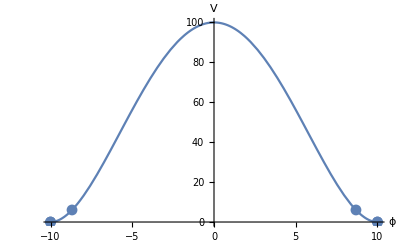

ϕ0 = 8.68529

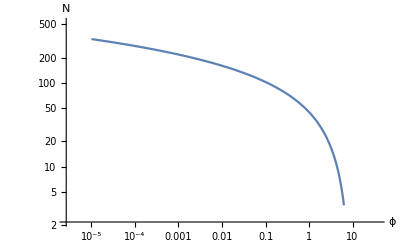

ReplaceAll::reps: {All} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

At n = 0, ϵ1 = (3 (ϕ'[0]/.All)^2)/((ϕ'[0]/.All)^2+(0.02 (-100+ϕ[0]^2)^2)/((0.01 (-100+ϕ[0]^2)^2)/(3-1/2 (ϕ'[0]/.All)^2)/.All))/.All

-Graphics-

General::ivar: 60 is not a valid variable.

ns[60] = 1+(∂_60 ((3 (ϕ'[60]/.All)^2)/((ϕ'[60]/.All)^2+(0.02 (-100+ϕ[60]^2)^2)/((0.01 (-100+ϕ[60]^2)^2)/(3-1/2 (ϕ'[60]/.All)^2)/.All))/.All))/((3 (ϕ'[60]/.All)^2)/((ϕ'[60]/.All)^2+(0.02 (-100+ϕ[60]^2)^2)/((0.01 (-100+ϕ[60]^2)^2)/(3-1/2 (ϕ'[60]/.All)^2)/.All))/.All)-2 ((3 (ϕ'[60]/.All)^2)/((ϕ'[60]/.All)^2+(0.02 (-100+ϕ[60]^2)^2)/((0.01 (-100+ϕ[60]^2)^2)/(3-1/2 (ϕ'[60]/.All)^2)/.All))/.All)

r[60] = 16 ((3 (ϕ'[60]/.All)^2)/((ϕ'[60]/.All)^2+(0.02 (-100+ϕ[60]^2)^2)/((0.01 (-100+ϕ[60]^2)^2)/(3-1/2 (ϕ'[60]/.All)^2)/.All))/.All)

General::ivar: 0.00122571 is not a valid variable.

General::stop: Further output of General :: ivar will be suppressed during this calculation.

-Graphics-

```mathematica
ϕsol2=findϕsol[v,vp,ni,nf,ni2,nf2,n1guess,True,True];
{ns,r,ϵ2} = findNsR[v,vp,ϕsol2,ni2,nf2,True,True];
```

## Replicate Planck Plot

#### Hilltop Models

ϕ0list = {-6.61037,-5.,-5.,-3.78194,3.78194,5.,6.61037}

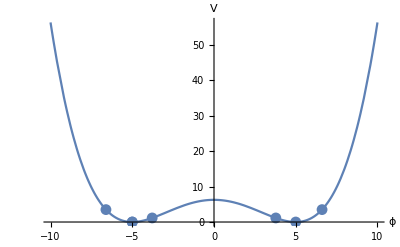

ϕ0 = 3.78194

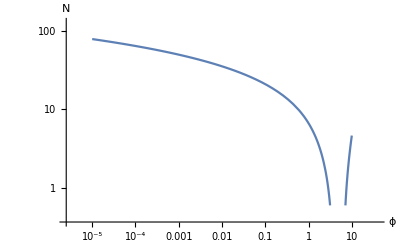

ϕi1 = 0.000192421

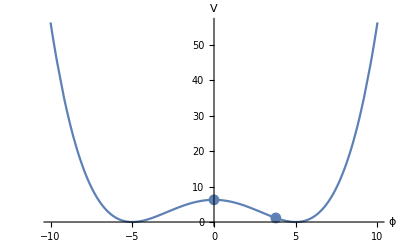

At n = 0, ϵ1 = 0.0551395

InterpolatingFunction::dmval: Input value {-20.2786} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-2.92786} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-4.72026} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

At n1 = -3.78289, ϵ1 = 1.

ϕi2 = 0.000343146

ϕpi2 = -0.0000522533

ϕsol2[60] = 0.000343146

At n = 0, ϵ1 = 1.46337

ns[60] = 0.695701

r[60] = 2.18433×10^-8

ϕ0list = {-11.5137,-10.,-10.,-8.68529,8.68529,10.,10.,11.5137}

-Graphics-

ϕ0 = 8.68529

-Graphics-

ϕi1 = 0.541141

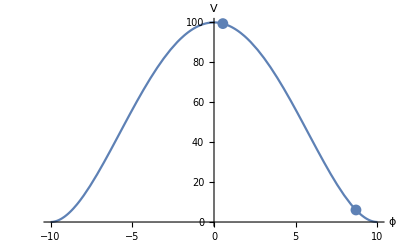

At n = 0, ϵ1 = 0.215158

At n1 = -1.60518, ϵ1 = 1.

ϕi2 = 0.576752

ϕpi2 = -0.0228457

ϕsol2[60] = 0.576752

At n = 0, ϵ1 = 1.00001

ns[60] = 0.92033

r[60] = 0.00417541

ϕ0list = {-16.4807,-15.,-15.,-13.6523,13.6523,15.,15.,16.4807}

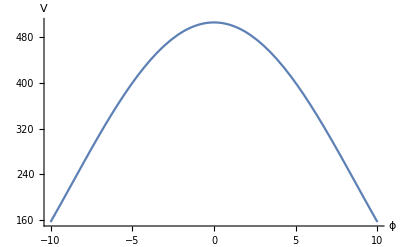

ϕ0 = 13.6523

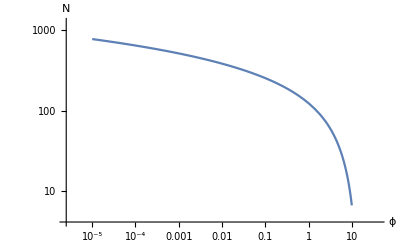

ϕi1 = 3.17548

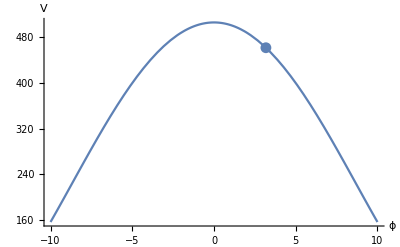

At n = 0, ϵ1 = 0.276295

At n1 = -1.28922, ϵ1 = 1.

ϕi2 = 3.2523

ϕpi2 = -0.0602704

ϕsol2[60] = 3.2523

At n = 0, ϵ1 = 1.

ns[60] = 0.956532

r[60] = 0.0290602

ϕ0list = {-21.4642,-20.,-20.,-18.6357,18.6357,20.,20.,21.4642}

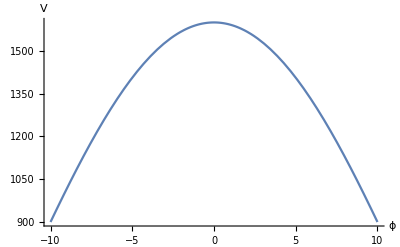

ϕ0 = 18.6357

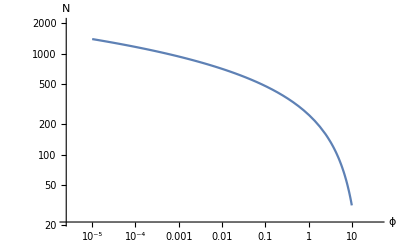

ϕi1 = 7.05055

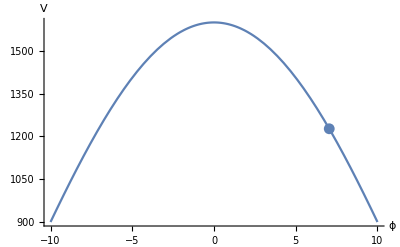

At n = 0, ϵ1 = 0.30142

At n1 = -1.19251, ϵ1 = 1.

ϕi2 = 7.14706

ϕpi2 = -0.0815443

ϕsol2[60] = 7.14706

At n = 0, ϵ1 = 0.999999

ns[60] = 0.964736

r[60] = 0.0531957

ϕ0list = {-26.4542,-25.,-25.,-23.6258,23.6258,25.,25.,26.4542}

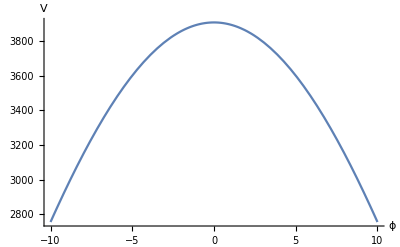

ϕ0 = 23.6258

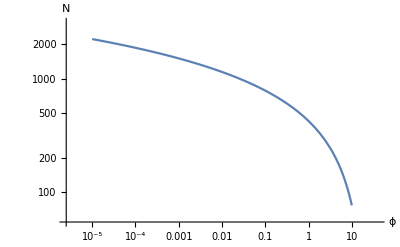

ϕi1 = 11.431

-Graphics-

At n = 0, ϵ1 = 0.314368

At n1 = -1.14952, ϵ1 = 1.

ϕi2 = 11.5378

ϕpi2 = -0.0934503

ϕsol2[60] = 11.5378

At n = 0, ϵ1 = 0.999954

ns[60] = 0.967164

r[60] = 0.0698636

```mathematica
σList = {5,10,15,20,25};
ns60List={};ns50List={};r60List={};r50List={};
Do[
v[x_]:=(0.01)*((x^2-(σ)^2)^2 );
vp[x_]=v'[x];
vpp[x_] = v''[x];

ni = 60; (* initial value f n for integration *)
nf = -1.8; (* final value of n for integration *)
ni2 = 60;
nf2 = 0;
n1guess = -1;

ϕsol2=findϕsol[v,vp,ni,nf,ni2,nf2,n1guess,False,True];
{ns,r,ϵ2} = findNsR[v,vp,ϕsol2,ni2,nf2,False,True]; 
AppendTo[ns60List,ns/.{n->60}];
AppendTo[ns50List,ns/.{n->50}];
AppendTo[r60List,r/.{n->60}];
AppendTo[r50List,r/.{n->50}];
,{σ,σList}]
```

{0.695701,0.92033,0.956532,0.964736,0.967164}

{2.18433×10^-8,0.00417541,0.0290602,0.0531957,0.0698636}

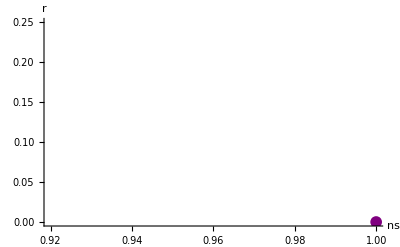

```mathematica
ns60List
r60List
nsmin = 0.92; nsmax = 1; rmin = 0; rmax = 0.25;
p1 = ListPlot[{ns60List,r60List},PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotMarkers->{●,12},PlotStyle->Purple,PlotLegends->PointLegend[Automatic,{"Hilltop at N=60"},LegendFunction->"Frame"]];
Show[p1]
```

ϵsr[0] = 2.32019

ϵsr[60] = 1.43448×10^-9

ϵsrL[0] = 1.52277

ϵsrL[60] = 1.36523×10^-9

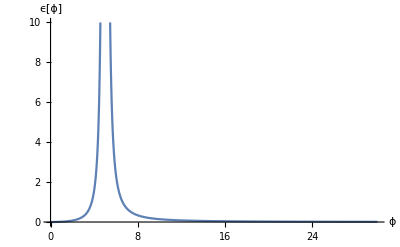

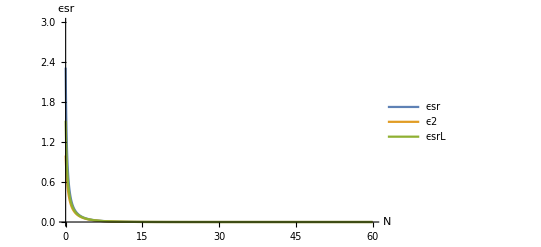

ηsr[0] = 1.80199

ηsr[60] = -0.16

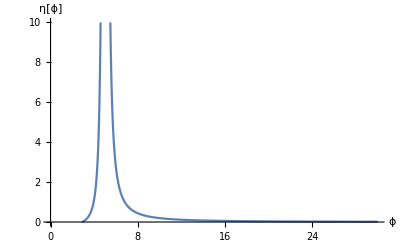

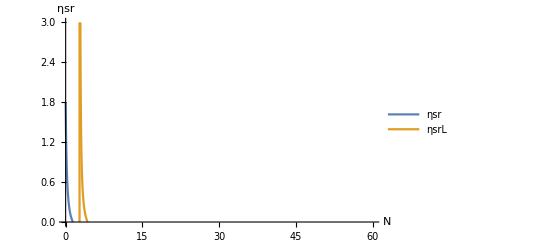

-Graphics-

ns[60] = 0.695693 and r[60] = 2.07894×10^-8

ns[50] = 0.695632 and r[50] = 4.36991×10^-7

```mathematica
{ϵsr,ηsr,ηsrL} = findSRparams[v,vp,vpp,ϕsol2,ni2,nf2,True,True];
Plot[{Legended[Evaluate[ηsr[n]],"ηsr"],Legended[Evaluate[ηsrL[n]],"ηsrL"]},{n,nf2,ni2},AxesLabel->{N,"ηsr"},PlotRange->{{nf2,ni2},{0,3}}]
(* Plots,Prints *)
Print["ns[60] = ",ns/.{n->60}," and r[60] = ",r/.{n->60}];
Print["ns[50] = ",ns/.{n->50}," and r[50] = ",r/.{n->50}];
```

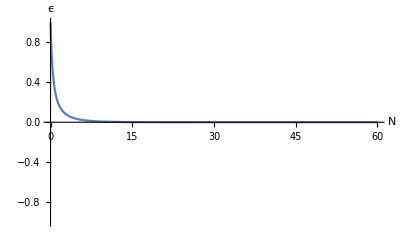

FindRoot::reged: The point {60.} is at the edge of the search region {0., 60.} in coordinate 1 and the computed search direction points outside the region.

General::stop: Further output of FindRoot :: reged will be suppressed during this calculation.

{60.}

number of zeros for ϵ is 0

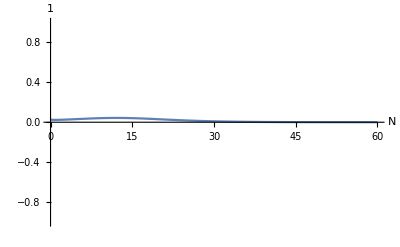

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

{0.876271,60.}

number of zeros for 1th derivative of ϵ is 1

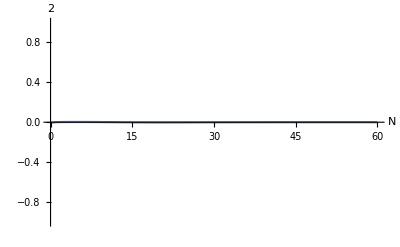

{0.876312,12.0831,60.}

number of zeros for 2th derivative of ϵ is 2

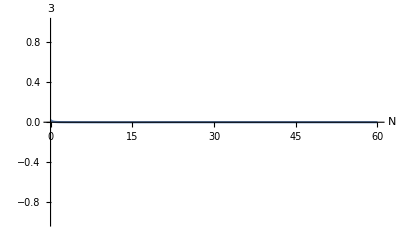

{4.90362,4.97852,20.2362,29.6657,41.6202,42.2048,49.3348,49.5194,49.704,56.6587,56.8388,57.019,57.613,58.8544,59.2322,59.6099,59.9959}

number of zeros for 3th derivative of ϵ is 17

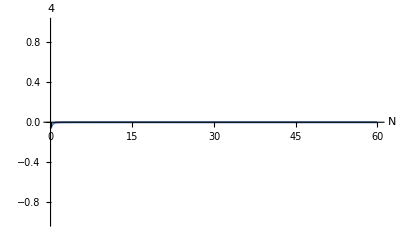

```mathematica
Zϵ = findZϵ[v,ϕsol2,nf2,ni2,0.1,3];
Print["Zϵ = ",Zϵ];
```

```mathematica
Zη = countAllZeros[v,vpp,ηsr,nf2,ni2,0.1,5];
Print["Zη = ",Zη];
```

```mathematica
Zϵ = findZϵ[ϕsol,nf2,ni2,0.1,5];
Print["Zϵ = ",Zϵ];
```

```mathematica
Zη = findZη[ϕsol,nf2,ni2,0.1,5];
Print["Zη = ",Zη];
```

```mathematica
MaxValue[ϵsr[n],n]
Plot[Evaluate[ϵsr[n]],{n,0,80},AxesLabel->{N,"ϵsr"},PlotRange->{0,2}]
f1[n_]=D[ϵsr[n],{n,1}];
Plot[Evaluate[f1[n]],{n,0,80},AxesLabel->{N,"ϵsr1"},PlotRange->{-1,1}]
f2[n_]=D[ϵsr[n],{n,2}];
MaxValue[f2[n],n]
Plot[Evaluate[f2[n]],{n,0,80},AxesLabel->{N,"ϵsr2"},PlotRange->{-1,1}]
```

```mathematica
Plot[Evaluate[ηsr[n]],{n,0,80},AxesLabel->{N,"ηsr1"}]
f1[n_]=D[ηsr[n],{n,1}];
Plot[Evaluate[f1[n]],{n,0,80},AxesLabel->{N,"ηsr1"}]
f2[n_]=D[ηsr[n],{n,2}];
Plot[Evaluate[f2[n]],{n,0,80},AxesLabel->{N,"ηsr2"}]
```

## Monomial Loop for Planck Plot

```mathematica
(* Loop over several monomial potentials and generate and ns vs r plot *)
ni = 80; nf = -1.2; ni2 = 80; nf2 = 0; n1guess = -1;
pList = {2,2/3,1,3,4};plotList = {}; 
clrList = {Black,Red,Yellow,Green,Purple}; ii=1;
nsmin = 0.92; nsmax = 1; rmin = 0; rmax = 0.35
Do[
Clear[v,vp,ns,r];
v[ϕ_] := ϕ^p;
vp[x_]=v'[x];
vpp[x_] = v''[x];
{ns,r} = findNsR[v,vp,vpp,ni,nf,ni2,nf2,n1guess,False,False];
AppendTo[plotList,ListPlot[Thread[{{ns/.{n->50}},{r/.{n->50}}}],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotMarkers->{●,12},PlotStyle->clrList[[ii]],PlotLegends->PointLegend[Automatic,{"N=50"},LegendFunction->"Frame"]]];
AppendTo[plotList,ListPlot[Thread[{{ns/.{n->60}},{r/.{n->60}}}],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotMarkers->{●,20},PlotStyle->clrList[[ii]],PlotLegends->PointLegend[Automatic,"N=60",LegendFunction->"Frame"]]];
AppendTo[plotList,ListLinePlot[Legended[{{ns/.{n->50},r/.{n->50}},{ns/.{n->60},r/.{n->60}}},V∝ϕ^pList[[ii]]],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotStyle->clrList[[ii]]]];
ii = ii+1,{p,pList}]
Show[plotList]
```

0.35

Set::shape: Lists {ns, r} and findNsR[v, vp, vpp, 80, -1.2, 80, 0, -1, False, False] are not the same shape.

General::stop: Further output of Set :: shape will be suppressed during this calculation.

-Graphics-